# Calculating non M=0 minima

Defining the lattice vectors dot product with reciprocal lattice vectors.

```mathematica
Clear[kx];
Clear[ky];
n1[kx_,ky_]:=-kx*Sqrt[3]/2+(3/2)*ky
n2[kx_,ky_]:=kx*Sqrt[3]/2+(3/2)*ky
```

Defining the magnitude of dispersion bands:

```mathematica
gamma0mag[Cp_,Cz_,kx_,ky_]:= Sqrt[(Cz+Cp*(Cos[n1[kx,ky]]+Cos[n2[kx,ky]]))^2 + (Cp*(Sin[n1[kx,ky]]+Sin[n2[kx,ky]]))^2]

gammaZmag[Bp_,Bz_,P1_,P_,K1_,kx_,ky_] := Sqrt[((1+P+K1*(1+P1))*Bz+Bp*K1*(1+P1)*(Cos[n1[kx,ky]]+Cos[n2[kx,ky]]))^2+(Bp*K1*(1+P1)*(Sin[n1[kx,ky]]+Sin[n2[kx,ky]]))^2]

gammaXmag[P1_,K1_,Bp_,Bz_,kx_,ky_] := Sqrt[(Bp((1+K1)*Cos[n1[kx,ky]]+K1*Cos[n2[kx,ky]])+K1*Bz)^2 +(Bp*((1+K1)*Sin[n1[kx,ky]]+K1*Sin[n2[kx,ky]]))^2]

gammaYmag[P1_,K1_,Bp_,Bz_,kx_,ky_] := Sqrt[(Bp((1+K1)*Cos[n2[kx,ky]]+K1*Cos[n1[kx,ky]])+K1*Bz)^2 +(Bp*((1+K1)*Sin[n2[kx,ky]]+K1*Sin[n1[kx,ky]]))^2]

E0[P1_,K1_,P_,M_,Bp_,Bz_,a1_,a2_]:=2*Bp*a1+Bz*a2+M^2/(3K1*(1+P1)+1+P)
```

Defining:
function in latex = Mathematica defined function
|γ_0-γ_z|^2 = gamma0Zmag2
|γ_x-γ_y|^2 =gammaXYmag2

-Graphics-

```mathematica
gamma0Zmag2[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,kx_,ky_] :=(Cz-(1+P+K1*(1+P1))*Bz+(Cp-Bp*K1*(1+P1))*(Cos[n1[kx,ky]]+Cos[n2[kx,ky]]))^2+((Cp-Bp*K1(1+P1))(Sin[n1[kx,ky]]+Sin[n2[kx,ky]]))^2

gammaXYmag2[Bp_,kx_,ky_]:= (Bp(Cos[n1[kx,ky]]-Cos[n2[kx,ky]]))^2+(Bp(Sin[n1[kx,ky]]-Sin[n2[kx,ky]]))^2
```

Defining the eigenvalues for non 0 Magnetisation:
-Graphics-
-Graphics-

```mathematica
(*gamma0mag[Cp,Cz,kx,ky]
gammaZmag[Bp,Bz,P1,P,K1,kx,ky] 
gammaXmag[P1,K1,Bp,Bz,kx,ky]
gammaYmag[P1,K1,Bp,Bz,kx,ky]
gamma0Zmag2[P1,P,K1,Cp,Cz,Bp,Bz,kx,ky]
gammaXYmag2[Bp,kx,ky]*)

eigen1[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,M_,L_,kx_,ky_]:= Sqrt[(gamma0mag[Cp,Cz,kx,ky]^2+gammaZmag[Bp,Bz,P1,P,K1,kx,ky] ^2)/2 + (M-L)^2 + 
Sqrt[((gamma0mag[Cp,Cz,kx,ky]^2-gammaZmag[Bp,Bz,P1,P,K1,kx,ky]^2 )/2 )^2+((M-L)^2)*gamma0Zmag2[P1,P,K1,Cp,Cz,Bp,Bz,kx,ky]]];

eigen2[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,M_,L_,kx_,ky_]:= Sqrt[(gamma0mag[Cp,Cz,kx,ky]^2+gammaZmag[Bp,Bz,P1,P,K1,kx,ky] ^2)/2 + (M-L)^2 - 
Sqrt[((gamma0mag[Cp,Cz,kx,ky]^2-gammaZmag[Bp,Bz,P1,P,K1,kx,ky]^2 )/2 )^2+((M-L)^2)*gamma0Zmag2[P1,P,K1,Cp,Cz,Bp,Bz,kx,ky]]];

eigen3[P1_,K1_,Bp_,Bz_,L_,kx_,ky_]:=Sqrt[(gammaXmag[P1,K1,Bp,Bz,kx,ky]^2+gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2+L^2+
Sqrt[((gammaXmag[P1,K1,Bp,Bz,kx,ky]^2-gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2)^2+L^2*gammaXYmag2[Bp,kx,ky]]];

eigen4[P1_,K1_,Bp_,Bz_,L_,kx_,ky_]:=Sqrt[(gammaXmag[P1,K1,Bp,Bz,kx,ky]^2+gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2+L^2-
Sqrt[((gammaXmag[P1,K1,Bp,Bz,kx,ky]^2-gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2)^2+L^2*gammaXYmag2[Bp,kx,ky]]];

Eigensum2[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,M_,L_,kx_,ky_]:=eigen1[P1,P,K1,Cp,Cz,Bp,Bz,M,L,kx,ky]+eigen2[P1,P,K1,Cp,Cz,Bp,Bz,M,L,kx,ky]+eigen3[P1,K1,Bp,Bz,L,kx,ky]+eigen4[P1,K1,Bp,Bz,L,kx,ky];
```

```mathematica
Clear[P1];
Clear[P];
Clear[K1];
Clear[M];
Clear[L];
(*Simplify[Eigensum[P1,P,K1,Cp,Cz,Bp,Bz,M,L,kx,ky]]*)
Eigensum[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,M_,L_,kx_,ky_]:=1/(√2)(√2 √(Bp^2+2 Bp^2 K1+2 Bp^2 K1^2+Bz^2 K1^2+L^2+2 Bp^2 K1 (1+K1) Cos[√3 kx]+2 Bp Bz K1 (1+2 K1) Cos[(√3 kx)/2] Cos[(3 ky)/2]-√(Bp^2 (-1+Cos[√3 kx]) (-Bz^2 K1^2-2 L^2+Bz^2 K1^2 Cos[3 ky])))+√2 √(Bp^2+2 Bp^2 K1+2 Bp^2 K1^2+Bz^2 K1^2+L^2+2 Bp^2 K1 (1+K1) Cos[√3 kx]+2 Bp Bz K1 (1+2 K1) Cos[(√3 kx)/2] Cos[(3 ky)/2]+√(Bp^2 (-1+Cos[√3 kx]) (-Bz^2 K1^2-2 L^2+Bz^2 K1^2 Cos[3 ky])))+√(2 (L-M)^2+(Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2+4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2-2 √(1/4 ((Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2-(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2-4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2)^2+(L-M)^2 ((Cz-Bz (1+K1+P+K1 P1)+2 (Cp-Bp K1 (1+P1)) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 (Cp-Bp K1 (1+P1))^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2)))+√(2 (L-M)^2+(Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2+4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2+2 √(1/4 ((Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2-(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2-4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2)^2+(L-M)^2 ((Cz-Bz (1+K1+P+K1 P1)+2 (Cp-Bp K1 (1+P1)) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 (Cp-Bp K1 (1+P1))^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2))))
```

Now defining the energy:

```mathematica
Energy [P1_,P_,K1_,A1_,A2_,Bp_,Bz_,M_,L_]:= -1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[Eigensum[P1,P,K1,A1,A2,Bp,Bz,M,L,kx,ky],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[Eigensum[P1,P,K1,A1,A2,Bp,Bz,M,L,kx,ky],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[Eigensum[P1,P,K1,A1,A2,Bp,Bz,M,L,kx,ky],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}])+E0[P1,K1,P,M,Bp,Bz,A1,A2]
```

Defining the Function F, which is a derivative of the sum of eigenvalues with respect to a mean field parameter

```mathematica
FBp[kx_,ky_,i_]:=(D[Eigensum[P1,P,K1,cp[[i]],cz[[i]],Bp,bz[[i]],m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Bp]/. Bp->bp[[i]]);
FBz[kx_,ky_,i_]:= (D[Eigensum[P1,P,K1,cp[[i]],cz[[i]],bp[[i]],Bz,m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Bz]/. Bz->bz[[i]]);
FA1[kx_,ky_,i_]:= (D[Eigensum[P1,P,K1, Cp,cz[[i]],bp[[i]],bz[[i]],m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Cp]/. Cp->cp[[i]]);
FA2[kx_,ky_,i_]:=(D[Eigensum[P1,P,K1,cp[[i]], Cz,bp[[i]],bz[[i]],m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Cz]/. Cz->cz[[i]]);
FM[kx_,ky_,i_]:=(D[Eigensum[P1,P,K1,cp[[i]], cz[[i]],bp[[i]],bz[[i]],M,l[[i]],kx,ky],M]/. M->m[[i]]*(3K1*(1+P1)+1+P));
FL[kx_,ky_,P1_,K1_,l_,i_]:=(D[(eigen3[P1,K1,bp[[i]],bz[[i]],L,kx,ky] +eigen4[P1,K1,bp[[i]],bz[[i]],L,kx,ky]),L]/. L->l);
```

## Now we have defined all the functions we may start calculating the mean field parameters

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

$Aborted

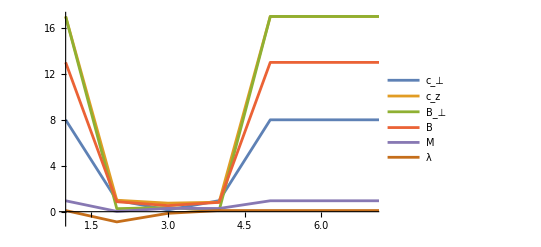

Final MFT Parameters:c_⊥ =0.150381, c_z=0.150381, B_⊥=0.368052TraditionalForm`0.531718, M=0.292041, m=0.292041, λ=-0.142295

Penultimate MFT Parameters:c_⊥ =0.150381, c_z=0.744379, B_⊥=0.264341TraditionalForm`0.866433, M=0.0261548, m=0.0261548, λ=-0.888957

```mathematica
loop=10;
Clear[cp];
Clear[cz];
cp= ConstantArray[8,loop];
cz = ConstantArray[17,loop];
bp=ConstantArray[17,loop];
bz=ConstantArray[13,loop];
m=ConstantArray[0.95,loop];
l=ConstantArray[0.1,loop];
P1=0;
P=0;
K1=0;
For[i=1,i<=loop-1,i++,
m[[i+1]]=(1/2)*(1/(2*(8*(Pi)^2/(3*Sqrt[3]))))* (NIntegrate[FM[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FM [kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FM[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}])(*this is unscaled magnetisation*);

cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBp [kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBp[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBz[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+
NIntegrate[FBz[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FA1[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FA1[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FA1[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FA2[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FA2[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FA2[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);
Clear[l1];
Clear[m2];
l1=Range[-5,5,0.2];
m2 = Range[-5,5,0.2];
For[j=1,j<=Length[l1],j++,
m2[[j]] =-(1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))*(NIntegrate[FL[kx,ky,P1,K1,l1[[j]],i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FL[kx,ky,P1,K1,l1[[j]],i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FL[kx,ky,P1,K1,l1[[j]],i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);
];
g=ListInterpolation[l1,m2];
magnetisation=Abs[m[[i+1]]];

l[[i+1]]=g[m[[i+1]]] (*this is unscaled magnetisation*);
]
final=i;

ListLinePlot[{cp,cz,bp,bz,m,l},PlotLegends->{"c_⊥ ","c_z","B_⊥","B","M","λ"},PlotRange->{{1,7},Full}]
Print["Final MFT Parameters:","c_⊥ =",cp[[final]] ,", c_z=",cp[[final]],", B_⊥=", bp[[final]],"TraditionalForm`", bz[[final]], ", M=", m[[final]]*(3K1*(1+P1)+1+P),", m=", m[[final]], ", λ=", l[[final]]]
z=final-1;
Print["Penultimate MFT Parameters:","c_⊥ =",cp[[final]] ,", c_z=",cz[[final]] ,", B_⊥=", bp[[z]],"TraditionalForm`", bz[[z]], ", M=", m[[z]]*(3K1*(1+P1)+1+P),", m=", m[[z]], ", λ=", l[[z]]]
```

```mathematica
Energyval=ConstantArray[0,final-1];
For[n=1,n<final,n++,
Energyval[[n]] = Energy [P1,P,K1,cp[[n]],cz[[n]],bp[[n]],bz[[n]], m[[n]]*(3K1*(1+P1)+1+P),l[[n]]]
]
ListPlot[Energyval,PlotRange->Full,PlotLegends->{"Energy"}, AxesLabel->{"Iteration step", "Energy Value"}]
If[Energyval[[final-2]]*0.9999<=Energyval[[final-2]]<=Energyval[[final-2]]*1.0001,
Print["Energy has converged, the converged energy value is "]
]
Print[ Energyval[[final-1]]]
```

-Graphics-

-1.41489×10^16